## Atomic to Physical Unit Conversions

```mathematica
(* Converting Atomic Units into Lab Units *)
Module[{enAU,enAU1GHz,tAU,tAU1ns,fAU,fAU1mVcm},
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."];

(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
Print["1 ns = ",tAU1ns, " A.U."];

(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
Print["1 mV/cm = ",fAU1mVcm," A.U."];

(* Association *)
au=Association[{"GHz"->enAU1GHz,"ns"->tAU1ns,"mVcm"->fAU1mVcm}]
];
```

1 GHz Photon Energy = 1.51983×10^-7 A.U.

1 ns = 4.13414×10^7 A.U.

1 mV/cm = 1.94469×10^-13 A.U.

```mathematica
au["GHz"]
au["ns"]
au["mVcm"]
```

1.51983×10^-7

4.13414×10^7

1.94469×10^-13

## Solver and Helper Functions

```mathematica
solver=Function[
{ic,fields,timing}, (* ic, fields, timing *)
(* A solver based only on initial conditions,physical conditions and start and stop times. *)
Module[{sol,x0,z0,vx0,vz0,fpulse,fmw,ω,α,toff,τring,t0,tmax},
ClearAll[x,z,t];
(* Unpack *)
{x0,z0,vx0,vz0}=ic;
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
(* solve *)
sol=NDSolve[
{
x''[t]==-x[t]/(x[t]^2+z[t]^2)^(3/2), (* -r/r^3 *)
x'[t0]==vx0,
x[t0]==x0,
z''[t]==-z[t]/(x[t]^2+z[t]^2)^(3/2) (* -r/r^3 *)
-fpulse*If[t<toff,1,0] (* Field that switches off *)
-fmw*Sin[ω*t+α]*If[t<toff,1,E^(-(t-toff)/τring)], (* MW that rings down *)
z'[t0]==vz0,
z[t0]==z0
},
{x,z},{t,t0,tmax},AccuracyGoal->13,PrecisionGoal->13,MaxSteps->1000000
];
(* return *)
sol]
];
```

```mathematica
icstarting=Function[
{w0,l0,θLRL,dL},
(* For starting the simulation with known energy, angular momentum, orientation, and angular momentum direction *)
(* r0 and v0 from initial energy *)
If[w0==0,
r0=l0^2/2;
v0=2/l0;
,
r0=(-1+√(1+2*w0*l0^2))/(2*w0);
v0=(1+√(1+2*w0*l0^2))/l0;
];
(* Orient r and v based on θLRL and dL *)
x0=r0*Sin[θLRL];
z0=-r0*Cos[θLRL];
vx0=dL*v0*Cos[θLRL];
vz0=dL*v0*Sin[θLRL];
{x0,z0,vx0,vz0}];
```

```mathematica
icskip=Function[
{bc,fields,ts,θLRL},
Module[{xf,zf,vxf,vzf,fpulse,fmw,ω,α,xi,zi,wf,Δw,wi,θvf,vi,vxi,vzi},
(* Unpack *)
{xf,zf,vxf,vzf}=bc;
{fpulse,fmw,ω,α}=fields;
(* Position *)
xi=xf;
zi=zf;
(* Energy *)
wf=wfunc[xf,zf,vxf,vzf];
Δw=wslingshot[ts,fmw,ω,α,θLRL];
wi=wf+Δw;
(* Velocity *)
θvf=ArcTan[vxf,vzf];
vi=√(2*(wi+1/√(xi^2+zi^2)));
{vxi,vzi}={vi*Cos[θvf+π],vi*Sin[θvf+π]};
{xi,zi,vxi,vzi}]
];
timeskip=Function[{sol,fields},
Module[{ts,fpulse,fmw,ω,α},
(* Unpack *)
{fpulse,fmw,ω,α}=fields;
ts=sol[[1,2]]["Domain"][[1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
{ts,tminus,tplus}]
];
```

## Evaluation Functions

```mathematica
wfunc=Function[{x,z,vx,vz},
1/2*(vx^2+vz^2)-1/√(x^2+z^2)];
rfunc=Function[{x,z},
√(x^2+z^2)];
lfunc=Function[{x,z,vx,vz},
z*vx-x*vz];
wslingshot=Function[
{t,fmw,ω,α,θLRL},
-Cos[θLRL]*√3*3/2*fmw/ω^(2/3)*Cos[ω*t+α]
];
```

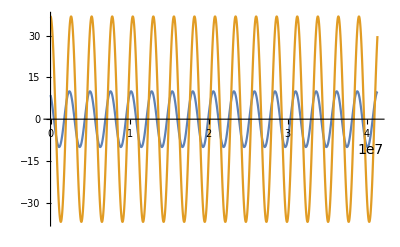

```mathematica
Plot[{10*Sin[ω*t+α],wslingshot[t,fmw,ω,θLRL,α]/au["GHz"]},{t,0,1*au["ns"]}]
```

## Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

## Test Case with No Field

### Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=1;
dL=1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.95*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
ic2=icskip[bc,fields,ts1,θLRL];
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

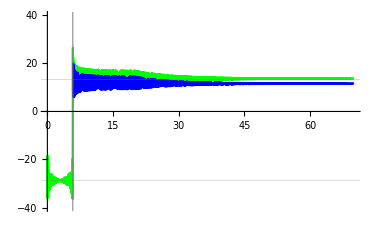

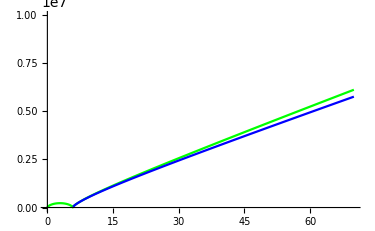

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue](**),
PlotRange->{All,{-40,40}},GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue],
PlotRange->{All,{0,10^7}}]
```

## Test Case 1 with No Field

### Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.95*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
ic2=icskip[bc,fields,ts1,θLRL];
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

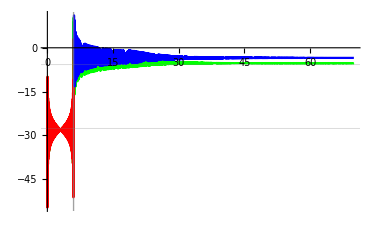

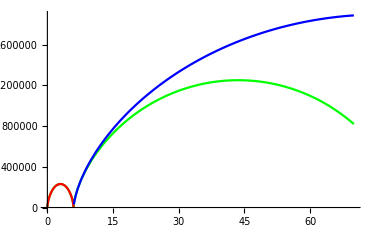

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue](**),
PlotRange->All,GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue]
]
```

## Test Case 2 with No Field

### Settings

```mathematica
(* IC *)
w0=-22*au["GHz"];
l0=√(3*(3+1));
θLRL=π;
dL=-1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6+π;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.95*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
ic2=icskip[bc,fields,ts1,θLRL];
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

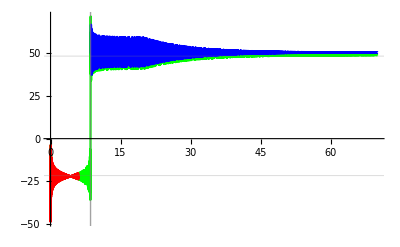

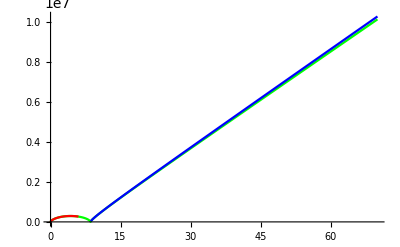

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue](**),
PlotRange->All,GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue]
]
```

## Test Case 3 with Field

### Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=10*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.233*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
ic2=icskip[bc,fields,ts1,θLRL];
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

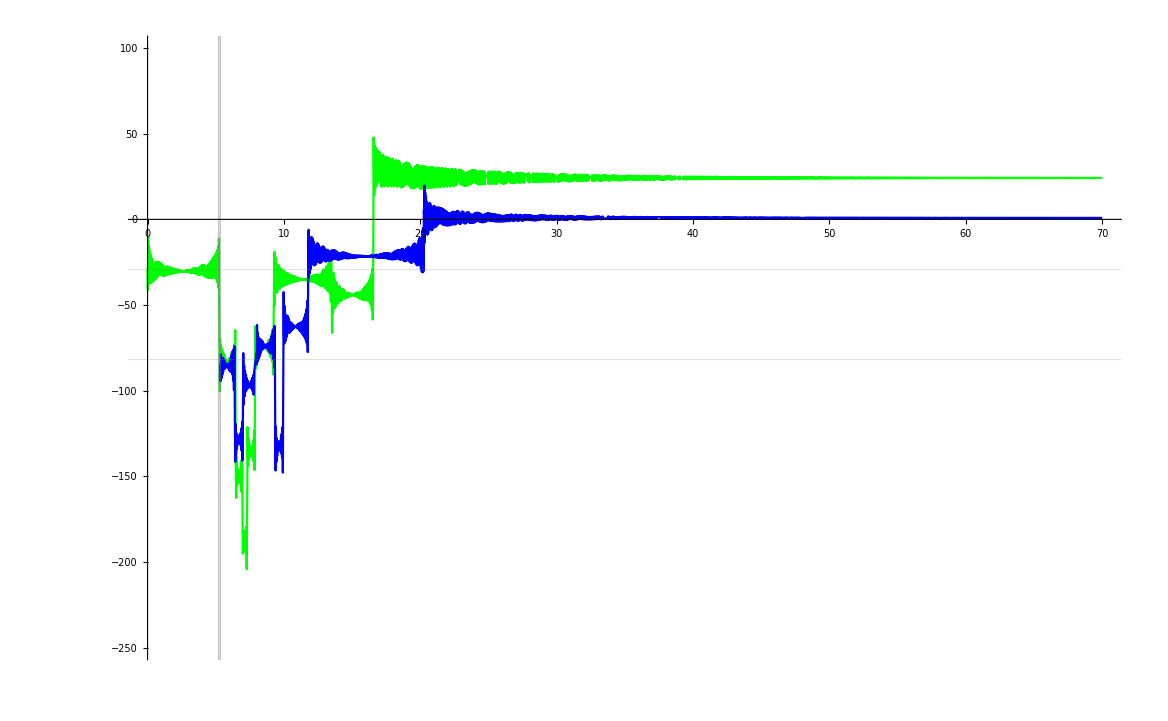

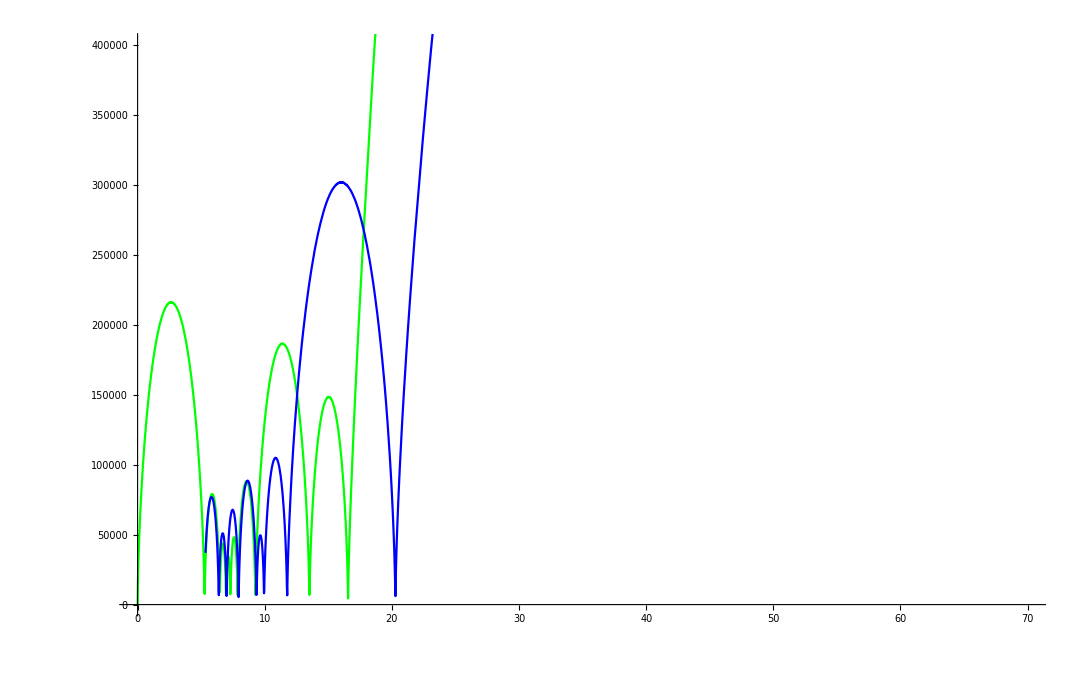

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue],
PlotRange->{All,{-250,100}},GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],
Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue],
PlotRange->{All,{0,4*10^5}}]
```

## Test Case 4 with Field

### Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=π;
dL=1;
(* Field parameters *)
fpulse=4*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.233*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
ic2=icskip[bc,fields,ts1,θLRL];
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

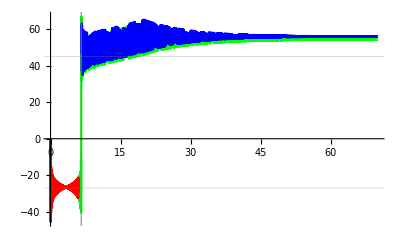

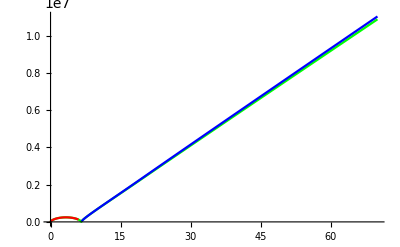

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue],
PlotRange->All,GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],
Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue],
PlotRange->All]
```